# SWIRP Mueller Matrix Model

## Mueller Matrix for Individual Elements

```mathematica
δ[λ_]:=2 π λ;

HOR[λ_]:={{1,0,0,0},{0,1,0,0},{0,0,Cos[δ[λ]],Sin[δ[λ]]},{0,0,-Sin[δ[λ]],Cos[δ[λ]]}}
lp=1/2{{1,0,1,0},{0,0,0,0},{1,0,1,0},{0,0,0,0}};
lpPath1=LP[45°];
lpPath2=LP[-45°];
QWP={{1,0,0,0},{0,0,0,-1},{0,0,1,0},{0,1,0,0}};
circHOR[λ_]:={{1,0,0,0},{0,1,0,0},{0,0,Cos[δ[λ]/2],Sin[δ[λ]/2]},{0,0,-Sin[δ[λ]/2],Cos[δ[λ]/2]}}
```

## Build Full Systems

```mathematica
systemMM[λ_]:=lp.HOR[λ].QWP
systemMMcirc[λ_]:=lp.circHOR[λ].HOR[λ].QWP
systemMMPath1[λ_]:=lpPath1.HOR[λ].QWP
systemMMPath2[λ_]:=lpPath2.HOR[λ].QWP
```

## Define Stokes Parameters

D is the degree of linear polarization, θ is the angle of linear polarization

```mathematica
stokes[D_,θ_]:={1,D Cos[2 θ],D Sin[2 θ],0};
stokes2[D_,θ_,λ_]:={1,D Cos[2 θ],D Sin[2 θ],0};
stokesi[D_,θ_,λ_]:={D Cos[2 θ]+λ,D Sin[2 θ]};
```

```mathematica
d = 0.5;
ϕ= π/4;
```

#### Plot input stokes vectors

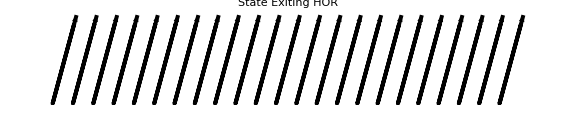

```mathematica
Graphics[Table[{Hue[-z/9+.4],Ellipse[StokesToJones[QWP.stokes[d,ϕ]],{3*z,0}]},{z,8,12.5,.2}],Axes->{False,False},PlotLabel->"State Exiting HOR",LabelStyle->Directive[ Black],ImageSize->Large]
```

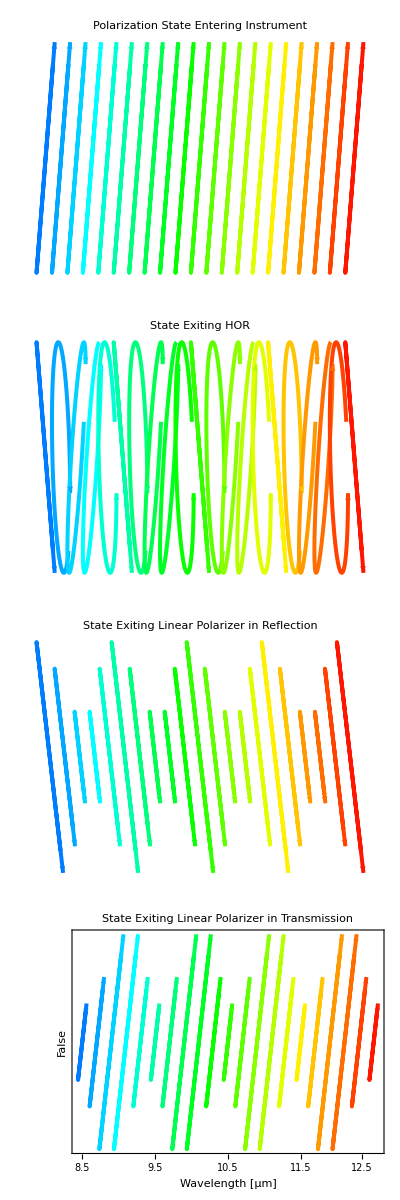

```mathematica
Framed[{Graphics[Table[Ellipse[StokesToJones[stokes[d,ϕ]],{3*z,0},Arrowheads->0.01,Opts`Color->Hue[-z/7  -.2]],{z,8.5,12.5,.2}],Axes->{False,False},PlotLabel->"Polarization State Entering Instrument",LabelStyle->Directive[ Black,12],ImageSize->Large]
,Graphics[Table[Ellipse[StokesToJones[HOR[z].QWP.stokes[d,ϕ]],{3*z,0},Arrowheads->0.01,Opts`Color->Hue[-z/7  -.2]],{z,8.5,12.5,.2}],Axes->{False,False},PlotLabel->"State Exiting HOR",LabelStyle->Directive[ Black,12],ImageSize->Large],
Graphics[Table[Ellipse[StokesToJones[lpPath2.HOR[z].QWP.stokes[d,ϕ]],{3*z,0},Arrowheads->0.01,Opts`Color->Hue[-z/7  -.2]],{z,8.5,12.5,.2}],Axes->{False,False},PlotLabel->"State Exiting Linear Polarizer in Reflection",LabelStyle->Directive[ Black,12],ImageSize->Large],
Graphics[Table[Ellipse[StokesToJones[lpPath1.HOR[z].QWP.stokes[d,ϕ]],{3*z,0},Arrowheads->0.01,Opts`Color->Hue[-z/7  -.2]],{z,8.5,12.5,.2}],PlotLabel->"State Exiting Linear Polarizer in Transmission",LabelStyle->Directive[ Black,12],ImageSize->Large,Axes->{True,False},AxesOrigin->{0,-1},Frame->{{False,False},{True,False}},FrameTicks->{{None,None},{{{25.5,8.5},{28.5,9.5},{31.5,10.5},{34.5,11.5},{37,12.5}},None}},FrameLabel->{{False,False},{"Wavelength [μm]",False}}]}//TableForm]
```

## Intensity at Detector

```mathematica
band=Subdivide[8.5,12.5,61];
```

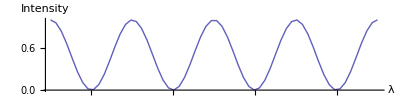

```mathematica
ListLinePlot[Table[{λ,(systemMM[λ].stokes[1,π/4])[[3]]},{λ,band}],ColorFunction->Function[{x,y},Hue[-x/1.5]],PlotStyle->Thick,AxesLabel->{"λ","Intensity"},AspectRatio->1/4]
```

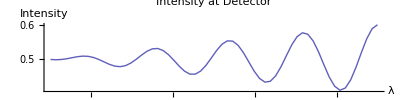

```mathematica
ListLinePlot[Table[{λ,(systemMM[λ].stokes[d[λ],θ[λ]])[[3]]},{λ,band}],ColorFunction->Function[{x,y},Hue[-x/1.5]],PlotStyle->Thick,ColorFunctionScaling->True,AxesLabel->{"λ","Intensity"},AspectRatio->1/4,PlotLabel->"Intensity at Detector",LabelStyle->Directive[Bold, Black]]
```

## Fourier Decomposition

The intensity spectrum is of the form

```mathematica
1/2(1+D[λ_]Cos[δ[λ]])
```

1/2 (1+Cos[2 π (-8.5+λ)] λ_)

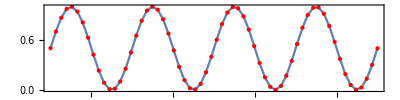

```mathematica
s1=Table[{λ,(systemMM[λ].{1,1,0,0})[[3]]},{λ,band}];
s2=Table[{λ,(systemMM[λ].{1,1,0,0})[[3]]},{λ,band}];

ListLinePlot[s1,AspectRatio->1/4,Mesh->All,MeshStyle->Directive[PointSize[Small],Red],Frame->True]
```

## Spectrogram

```mathematica
n=Dimensions[band][[1]];
```

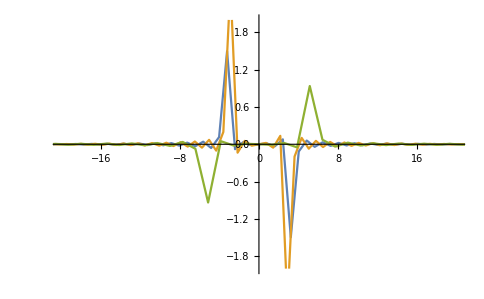

```mathematica
(*fieldValues=Table[(systemMM[λ].stokes[d[λ],θ[λ]])[[3]],{λ,band}];*)
fieldValues=Table[(systemMM[λ].stokes[d[λ],θ[λ]])[[3]],{λ,band}];
a1=Table[(systemMM[λ].stokes[.1,0])[[3]],{λ,band}];
a2=Table[(systemMM[λ].stokes[.2,π/8])[[3]],{λ,band}];
a3=Table[(systemMM[λ].stokes[.3,π/4])[[3]],{λ,band}];
getFourier[a_,n_]:=Module[{FFTValues,dp,dk,frequencyValues,FFTValues1},
FFTValues=Fourier[RotateLeft[a,n/2-1],FourierParameters ->{1,-1}];
FFTValues1=RotateRight[FFTValues,n/2-1];
dp=a[[2]]-a[[1]];
dk=1/(n*dp);
frequencyValues=Table[dk*(i-n/2),{i,1,n}];
Table[{frequencyValues[[i]],Im[FFTValues1[[i]]]},{i,1,n}]];

ListLinePlot[{getFourier[a1,n],getFourier[a2,n],getFourier[a3,n]},PlotRange->{{-20,20},{-2,2}}]
```

```mathematica
getFourier2[d_,θ_]:=Module[{a,FFTValues,dp,dk,frequencyValues,FFTValues1},
a=Table[(systemMM[λ].stokes[1,θ+d λ])[[3]],{λ,band}];
FFTValues=Fourier[RotateLeft[a,n/2-1],FourierParameters ->{1,-1}];
FFTValues1=RotateRight[FFTValues,n/2-1];
dp=a[[2]]-a[[1]];
dk=1/(n*dp);
frequencyValues=Table[dk*(i-n/2),{i,1,n}];
Table[{frequencyValues[[i]],Im[FFTValues1[[i]]]},{i,1,n}]];
getFourier3[d_,θ_]:=Module[{a,FFTValues,dp,dk,frequencyValues,FFTValues1},
a=Table[(systemMM[λ].stokes[1,θ+d λ])[[3]],{λ,band}];
FFTValues=Fourier[RotateLeft[a,n/2-1],FourierParameters ->{1,-1}];
FFTValues1=RotateRight[FFTValues,n/2-1];
dp=a[[2]]-a[[1]];
dk=1/(n*dp);
frequencyValues=Table[dk*(i-n/2),{i,1,n}];
Table[{frequencyValues[[i]],Re[FFTValues1[[i]]]},{i,1,n}]];
```

```mathematica
plot=Manipulate[ListLinePlot[{getFourier3[d,θ],getFourier2[d,θ]},PlotRange->{{-10,10},{-10,20}},Epilog->{Text[Style["d = " <> ToString[d] ,FontSize->14,Red],{8,12}],Text[Style["θ = " <> ToString[θ] <> " rad" ,FontSize->14,Red],{8,15}]},PlotLegends->{"Re","Im"}],{d,.1,.5,0.001},{θ,0,1.5,.01},AutorunSequencing->{{1,20},{2,20}}]
```

## Corrections to Real Spectral Artifacts

#### IR Intensity from Goddard

```mathematica
irPic=-Graphics- ;
irPic2=-Graphics-;
```

Looking up coordinates

```mathematica
irPic2
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
corners={{1486.6851183313279,913.6746891295629},{217.97753710389094,156.62695547533082}}
```

{{1486.69,913.675},{217.978,156.627}}

```mathematica
corners2={{496.53681419539043,209.2798286763206},{40.523149092392394,32.824597185396726}};
```

#### Affine Transformation, Matrix + Vector between pixels and plot coordinates

```mathematica
affine2=Solve[{{a11,a12},{a21,a22}}.corners2[[1]]+{of1,of2}=={0,0} &&
{{a11,a12},{a21,a22}}.{corners2[[1,1]],corners2[[2,2]]}+{of1,of2}=={0,100} &&
{{a11,a12},{a21,a22}}.corners2[[2]]+{of1,of2}=={22,100},{a11,a12,a21,a22,of1,of2}]
```

{{a11→-0.0482442,a12→0.,a21→0.,a22→-0.566716,of1→23.955,of2→118.602}}

```mathematica
affine=Solve[{{a11,a12},{a21,a22}}.corners[[1]]+{of1,of2}=={6.5,200} &&
{{a11,a12},{a21,a22}}.{corners[[1,1]],corners[[2,2]]}+{of1,of2}=={6.5,300} &&
{{a11,a12},{a21,a22}}.corners[[2]]+{of1,of2}=={27.5,300},{a11,a12,a21,a22,of1,of2}]
```

{{a11→-0.0165523,a12→0.,a21→0.,a22→-0.132092,of1→31.108,of2→320.689}}

```mathematica
pixelMat={{affine[[1,1,2]],affine[[1,2,2]]},{affine[[1,3,2]],affine[[1,4,2]]}};
pixelMat2={{affine2[[1,1,2]],affine2[[1,2,2]]},{affine2[[1,3,2]],affine2[[1,4,2]]}};
Round[pixelMat,.00001]//MatrixForm
Round[pixelMat2,.00001]//MatrixForm
offset={affine[[1,5,2]],affine[[1,6,2]]};
offset2={affine2[[1,5,2]],affine2[[1,6,2]]}
Round[offset,.001]//MatrixForm
Round[offset2,.001]//MatrixForm
```

(-0.01655 | 0.
0. | -0.13209)

(-0.04824 | 0.
0. | -0.56672)

{23.955,118.602}

(31.108
320.689)

(23.955
118.602)

```mathematica
pixelMat.corners[[1]]+offset
pixelMat.corners[[2]]+offset
```

{6.5,200.}

{27.5,300.}

```mathematica
pixelMat2.corners2[[1]]+offset2
pixelMat2.corners2[[2]]+offset2
```

{0.,0.}

{22.,100.}

#### Ger Coord Along Figure Trace

```mathematica
redcoord={{1473.4928359015946,808.0231594124537},{1441.2372713345947,810.9554834639991},{1353.2675497882308,810.9554834639991},{1306.3503649635034,805.0908353609082},{1278.4932864738214,788.9630530774082},{1262.3655041903214,287.53564026313427},{1237.440749752185,441.482652969271},{1218.3806434171395,387.2346580156799},{1194.9220510047758,316.85888077858885},{1187.591240875912,445.88113904658917},{1159.73416238623,632.0837163197259},{1134.8094079480938,774.3014328196808},{1126.0124357934574,783.0984049743172},{1089.3583851491392,762.572136613499},{1055.6366585563662,784.5645670000899},{974.9977471388661,679.0009011444533},{966.2007749842296,665.8054429124988},{922.2159142110477,586.6326935207712},{810.7876002523203,514.7907542579076},{790.2613318915019,632.0837163197259},{777.0658736595474,535.3170226187258},{750.6749571956382,453.2119491754528},{716.9532306028655,489.86599981977105},{667.1037217265925,552.9109669279985},{608.4572406956834,618.8882580877714},{604.0587546183651,677.5347391186806},{589.3971343606378,731.7827340722716},{587.9309723348651,734.7150581238171},{586.4648103090924,737.6473821753626},{571.803190051365,784.5645670000899},{555.675407767865,787.4968910516354},{533.6829773812741,786.0307290258627},{520.4875191493195,786.0307290258627},{491.1642786338648,783.0984049743172},{473.57033432459207,784.5645670000899},{469.17184824727383,758.1736505361808},{464.7733621699557,577.835721366135},{454.5102279895466,586.6326935207712},{410.52536721636466,780.1660809227718},{438.3824457060465,712.7226277372262},{435.4501216545011,746.444354329999},{429.58547355141013,778.6999188969991},{391.4652608813192,769.9029467423627},{368.00666846895547,762.572136613499},{347.48040010813725,758.1736505361808},{322.5556456700008,752.3090024330899},{285.90159502568247,737.6473821753626},{259.5106785617734,542.6478327475894},{265.37532666486425,671.6700910155897},{262.44300261331875,394.5654681445436},{255.11219248445514,353.51293142290706},{246.31522032981877,269.9416959538614},{238.98441020095515,240.61845543840684},{225.78895196900055,240.61845543840684}};
```

```mathematica
bluecoord={{1465.8010429201765,677.4235860409146},{1408.3698355395106,673.5078219013237},{1375.738467709587,672.2025671881267},{1318.307260328921,672.2025671881267},{1281.7601283594063,665.676293622142},{1272.6233453670277,665.676293622142},{1258.2655435218612,356.3309265944645},{1236.0762133975131,433.34095467308464},{1225.6341756919376,408.5411151223425},{1209.9711191335741,317.17328519855596},{1199.5290814279983,330.22583233052546},{1185.171279582832,434.6462093862816},{1178.6450060168472,540.3718411552347},{1146.0136381869233,613.4661050942639},{1113.3822703569997,647.4027276373847},{1048.119534697152,673.5078219013237},{1016.7934215804254,666.981548335339},{991.9935820296834,656.5395106297633},{986.7725631768955,652.6237464901725},{943.699157641396,608.2450862414762},{873.2154031287606,449.00401123144803},{849.7208182912156,418.98315282791816},{836.668271159246,408.5411151223425},{806.6474127557161,371.9939831528279},{746.6056959486564,370.68872843963095},{689.1744885679905,428.11993582029686},{639.5748094665063,480.3301243481749},{623.9117529081428,527.3192940232651},{618.690734055355,548.2033694344163},{617.3854793421581,552.1191335740073},{614.7749699157642,561.2559165663858},{603.0276774969917,587.3610108303249},{601.7224227837947,596.4977938227036},{599.1119133574008,599.1083032490975},{589.9751303650221,626.5186522262335},{580.8383473726435,646.0974729241877},{562.5647813878861,655.2342559165663},{531.2386682711593,653.9290012033695},{502.5230645808264,652.6237464901725},{479.0284797432813,650.0132370637787},{472.50220617729644,626.5186522262335},{468.58644203770564,580.8347372643402},{467.28118732450866,556.0348977135981},{459.44965904532694,546.8981147212194},{451.6181307661452,557.340152426795},{442.48134777376663,591.2767749699158},{433.34456478138793,625.2133975130365},{418.98676293622145,652.6237464901725},{398.1026875250702,653.9290012033695},{383.7448856799038,655.2342559165663},{370.69233854793424,651.3184917769755},{361.5555555555556,647.4027276373847},{332.83995186522264,643.4869634977938},{308.0401123144806,639.571199358203},{285.8507821901324,636.9606899318092},{280.6297633373446,569.0874448455676},{270.187725631769,501.2141997593261},{259.7456879261934,459.44604893702365},{250.6089049338147,318.47853991175293},{223.19855595667872,293.6787003610108}};
```

```mathematica
trans={{485.7648378543747,34.87640220273309},{457.03956761166614,47.187232306751014},{430.36610238629396,61.0369161737712},{410.87395472159886,73.86069753212323},{392.920660819906,51.80379359575775},{369.8378543748724,33.337548439730824},{351.3716092188455,32.824597185396755},{329.82765653681406,37.441158474403494},{319.56863145013244,65.65347746277794},{313.4132163981235,114.8967978788497},{311.36141138078716,153.36814195390576},{296.9987762594329,169.78258209259639},{306.23189883744635,169.2696308382623},{292.89516622476026,182.60636345094838},{277.50662859473783,188.76177850295738},{258.01448093004274,190.8135835202937},{250.83316336936556,187.22292473995512},{248.78135835202923,165.16602080358965},{246.21660208035885,125.15582296553131},{244.67774831735662,108.74138282684075},{239.5482357740158,75.39955129512546},{235.95757699367724,93.3528451968183},{234.418723230675,129.25943300020396},{231.34101570467053,184.6581684682847},{226.21150316132972,190.8135835202937},{214.41362431164583,185.1711197226188},{207.2323067509687,137.97960432388334},{210.3100142769732,166.70487456659188},{206.71935549663462,97.96940648582503},{200.56394044462564,53.34264735875999},{191.3308178666122,32.824597185396755},{165.17030389557405,32.824597185396755},{151.32062002855386,33.85049969406492},{147.72996124821532,88.22333265347748},{144.65225372221082,144.13501937589234},{136.44503365286553,180.55455843361207},{116.43993473383637,201.0726086069753},{85.14990821945744,203.6373648786457},{70.27432184376909,194.91719355496633},{60.52824801142156,182.60636345094838},{53.346930450744416,161.57536202325107},{49.243320416071775,136.9537018152152},{47.191515398735454,90.78808892514789},{46.67856414440137,34.87640220273309}};
```

#### Plot Results

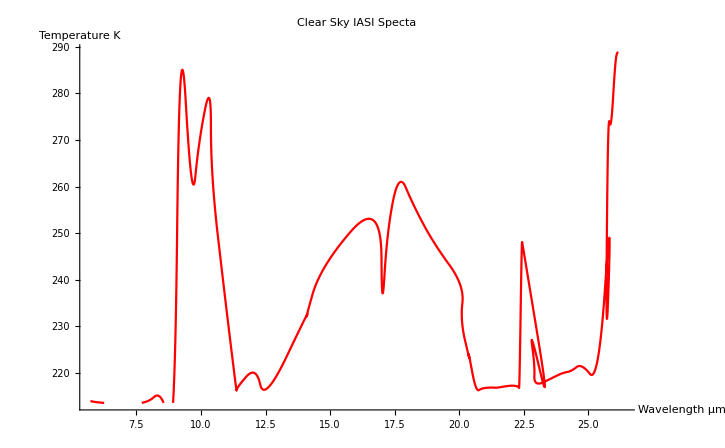

```mathematica
ListLinePlot[Map[pixelMat.# +offset-{1,0}&,redcoord],PlotStyle->{Red,PointSize[.01]},PlotLabel->"Clear Sky IASI Specta",InterpolationOrder->2,Method->"Spline",AxesLabel->{"Wavelength μm","Temperature K"}]
```

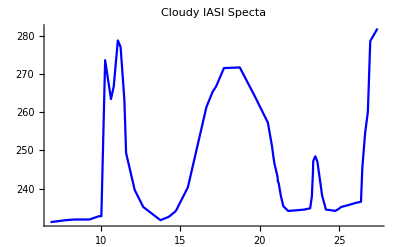

```mathematica
ListLinePlot[Map[pixelMat.# +offset&,bluecoord],PlotStyle->{Blue,PointSize[.01]},PlotLabel->"Cloudy IASI Specta",InterpolationOrder->1,Method->"Spline"]
```

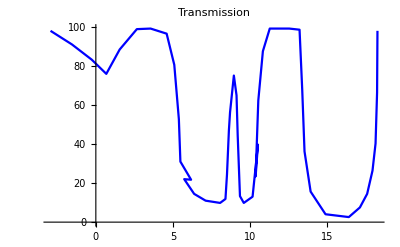

```mathematica
ListLinePlot[Map[pixelMat2.# +{20.5,118}&,trans],PlotStyle->{Blue,PointSize[.01]},PlotLabel->"Transmission"]
```

#### Interpolating Function

```mathematica
clearspec=Interpolation[Map[pixelMat.# +offset&,redcoord],InterpolationOrder->1, Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
cloudspec=Interpolation[Map[pixelMat.# +offset&,bluecoord],InterpolationOrder->1, Method->"Spline"]
o2trans=Interpolation[Map[pixelMat2.# +{20.5,118}&,trans],InterpolationOrder->1,Method->"Spline"]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

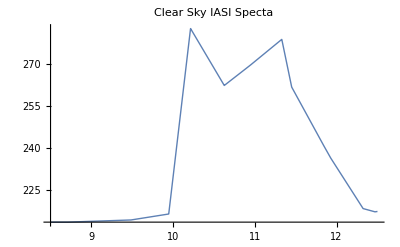

```mathematica
Plot[clearspec[ν],{ν,8.5,12.5},PlotLabel->"Clear Sky IASI Specta",PlotStyle->Thick]
```

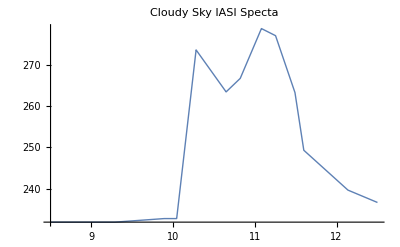

```mathematica
Plot[cloudspec[λ],{λ,8.5,12.5},PlotLabel->"Cloudy Sky IASI Specta",PlotStyle->Thick]
```

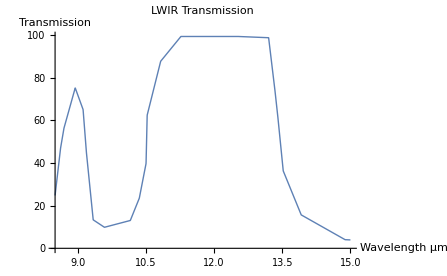

```mathematica
Plot[o2trans[λ],{λ,8.5,15},PlotLabel->"LWIR Transmission",PlotStyle->Thick,AxesLabel->{"Wavelength μm","Transmission"}]
```

Build function which takes in an intensity profile, corrects for the assumed intensity spectrum and and transmission data

#### Sensor Set Up

```mathematica
numberofpixels=61;
off=4.0/numberofpixels;
bandwidth=Subdivide[8.5+off/2,12.5+off/2,61];
```

Corrections to Irradaince Profile

#### Correction for Intensity Profile

First bin the profile accordingly. Then, normalize the transmission profile, and invert so each bin has a corrective multiplicative factor

```mathematica
ozonebin=Table[o2trans[λ],{λ,bandwidth}];
```

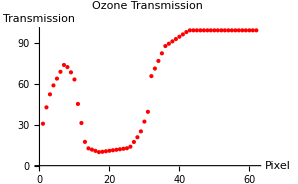

```mathematica
ListPlot[ozonebin,PlotLabel->"Ozone Transmission",AxesLabel->{"Pixel","Transmission"},PlotStyle->{Red,PointSize[.01]}]
```

#### Correction for QWP

Load from C:\Users\Kira Hart\Documents\SWIRP\Mathematica Files\Edmund IR QWR.nb

```mathematica
QWPtrans<<"QWPtrans.m";
```

Get::noopen: Cannot open QWPtrans.m.

```mathematica
QWPbin=Table[QWPtrans[λ],{λ,bandwidth}];
ListPlot[QWPbin,PlotLabel->"QWP Efficiency",AxesLabel->{"Pixel","Efficiency"},PlotStyle->{Red,PointSize[.01]}]
```

-Graphics-

#### Correction for Diffraction Grating

-Graphics-

```mathematica
gratingdata={{8.5,.75},{9,.85},{10,.9},{11,.925},{11.5,.85},{12.5,.8}};
```

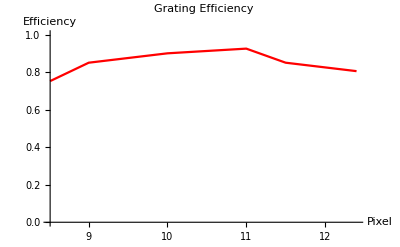

```mathematica
gratingEfficiency=Interpolation[gratingdata,InterpolationOrder->1];
Plot[gratingEfficiency[λ],{λ,8.51,12.4},PlotRange->{0,1},PlotLabel->"Grating Efficiency",AxesLabel->{"Pixel","Efficiency"},PlotStyle->Red ]
```

#### Correction for HOR

#### Correction for Microbolometer Response

Define New MM System Using Real Transmission

#### Description of non-Polarization Transmission Signals

## -Graphics-

```mathematica
QWPreal[λ_]:= QWPtrans[λ]*QWP;
```

```mathematica
QWPreal[8.5]//MatrixForm
```

(QWPtrans[8.5] | 0 | 0 | 0
0 | 0 | 0 | -QWPtrans[8.5]
0 | 0 | QWPtrans[8.5] | 0
0 | QWPtrans[8.5] | 0 | 0)

```mathematica
systemMMReal1[λ_]:=lpPath1.HOR[λ].QWPreal[λ]*gratingEfficiency[λ]*o2trans[λ]/100;
systemMMReal2[λ_]:=lpPath2.HOR[λ].QWPreal[λ]*gratingEfficiency[λ]*o2trans[λ]/100;
```

```mathematica
stokesi[d[9.5],θ[8.5],8.5]
```

{8.5+0.5[9.5] Cos[2 θ[8.5]],0.5[9.5] Sin[2 θ[8.5]]}

Part::partw: Part 3 of systemMMReal[8.5].{1,0.,0.8,0} does not exist.

Part::partw: Part 3 of systemMMReal[8.56557].{1,0.,0.8,0} does not exist.

Part::partw: Part 3 of systemMMReal[8.63115].{1,0.,0.8,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

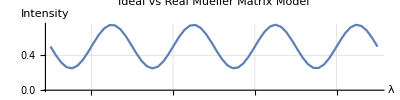

```mathematica
Framed[ListLinePlot[{Table[{λ,(systemMM[λ].stokes[0.5,0Degree])[[3]]},{λ,band}],Table[{λ,(systemMMReal[λ].stokes[0.8,45Degree])[[3]]},{λ,band}]},PlotStyle->{FontFamily-> Times,Thick},AxesLabel->{"λ","Intensity"},AspectRatio->1/4,PlotLabel->"Ideal vs Real Mueller Matrix Model",GridLines->Automatic,PlotLegends->{"Ideal MM", "Real MM"}]]
```

Define Functions

```mathematica
fieldValues=Table[(systemMM[λ].stokes[.7,π/10λ])[[3]],{λ,band}]
```

{0.783156,0.664492,0.512615,0.358191,0.2324,0.16064,0.157401,0.223335,0.345132,0.498197,0.651627,0.774442,0.841844,0.840224,0.769909,0.645097,0.490988,0.338699,0.218978,0.155998,0.162476,0.237104,0.364813,0.519817,0.670821,0.787334,0.845831,0.834501,0.755632,0.625148,0.469396,0.319823,0.206629,0.15267,0.168841,0.251876,0.38501,0.541362,0.689362,0.799128,0.848497,0.827501,0.740379,0.604722,0.44792,0.301634,0.1954,0.150668,0.17647,0.267596,0.405647,0.562748,0.70718,0.809781,0.849833,0.81925,0.724208,0.583895,0.426643,0.284203,0.185334,0.15}

```mathematica
(*returns 4 channels fourier transmorms*)
```

```mathematica
stft[array_,n_,dk_]:=Module[{fieldValues1,fieldValues2,fieldValues3,fieldValues4,n1,FFTValues1,FFTValues2,FFTValues3,FFTValues4,frequencyValues1},
fieldValues1=Part[array,1;;(n+2)/4];fieldValues2=Part[array,(n+2)/4;;(n+2)/2];fieldValues3=Part[array,(n+2)/2;;(n+2)/4+(n+2)/2];fieldValues4=Part[array,(n+2)/4+(n+2)/2;;n];
n1=Dimensions[fieldValues1][[1]];
FFTValues1=Fourier[RotateLeft[fieldValues1,n1/2-1],FourierParameters ->{1,-1}];
FFTValues2=Fourier[RotateLeft[fieldValues2,n1/2-1],FourierParameters ->{1,-1}];
FFTValues3=Fourier[RotateLeft[fieldValues3,n1/2-1],FourierParameters ->{1,-1}];
FFTValues4=Fourier[RotateLeft[fieldValues4,n1/2-1],FourierParameters ->{1,-1}];
FFTValues1=RotateRight[FFTValues1,n1/2-1];
FFTValues2=RotateRight[FFTValues2,n1/2-1];
FFTValues3=RotateRight[FFTValues3,n1/2-1];
FFTValues4=RotateRight[FFTValues4,n1/2-1];
frequencyValues1=Table[dk*(i-n1/2),{i,1,n1}];
Return[{Table[{frequencyValues1[[i]],Im[FFTValues1[[i]]]},{i,1,n1}],Table[{frequencyValues1[[i]],Im[FFTValues2[[i]]]},{i,1,n1}],Table[{frequencyValues1[[i]],Im[FFTValues3[[i]]]},{i,1,n1}],Table[{frequencyValues1[[i]],Im[FFTValues4[[i]]]},{i,1,n1-1}]}]];
```

```mathematica
result=stft[fieldValues,n,.1];
```

Part::span: 1;;(2+n)/4 is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: (2+n)/4;;(2+n)/2 is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: (2+n)/2;;(3 (2+n))/4 is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Fourier::fftl: Argument {0.783156,0.664492,0.512615,0.358191,0.2324,0.16064,0.157401,0.223335,0.345132,0.498197,«32»,0.740379,0.604722,0.44792,0.301634,0.1954,0.150668,0.17647,0.267596,«12»}⟦1;;«1»⟧ is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument {0.783156,0.664492,0.512615,0.358191,0.2324,0.16064,0.157401,0.223335,0.345132,0.498197,«32»,0.740379,0.604722,0.44792,0.301634,0.1954,0.150668,0.17647,0.267596,«12»}⟦«1»;;«1»⟧ is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

```mathematica
ListLinePlot[{result[[1]],result[[2]],result[[3]],result[[4]]},PlotRange->All]
```

-Graphics-

```mathematica
splitsignal[array_,n_]:=Module[{fieldValues1,fieldValues2,fieldValues3,fieldValues4,n1},
fieldValues1=Part[array,1;;(n+2)/4];fieldValues2=Part[array,(n+2)/4;;(n+2)/2];fieldValues3=Part[array,(n+2)/2;;(n+2)/4+(n+2)/2];fieldValues4=Part[array,(n+2)/4+(n+2)/2;;n];
n1=Dimensions[fieldValues1];
Return[{fieldValues1,fieldValues2,fieldValues3,fieldValues4}]];
```

```mathematica
signal=splitsignal[fieldValues,n];
ListLinePlot[{signal[[1]],signal[[2]],signal[[3]],signal[[4]]}]
```

Part::span: 1;;(2+n)/4 is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: (2+n)/4;;(2+n)/2 is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: (2+n)/2;;(3 (2+n))/4 is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

-Graphics-

```mathematica
getDOLP[array_]:= Module[{signalt,max1,min1,dolp,x,l},
signalt=Interpolation[array];
l=Dimensions[array][[1]];
max1=NMaximize[{signalt[x],1<x≤l},x,Method->"SimulatedAnnealing"][[1]];
min1=NMinimize[{signalt[x],1<x≤l},x,Method->"SimulatedAnnealing"][[1]];
Return[dolp=max1-min1]];
```

```mathematica
dolptest=Table[getDOLP[signal[[i]]],{i,1,4}]
```

Interpolation::innd: First argument in {0.783156,0.664492,0.512615,0.358191,0.2324,0.16064,0.157401,0.223335,0.345132,0.498197,«32»,0.740379,0.604722,0.44792,0.301634,0.1954,0.150668,0.17647,0.267596,«12»}⟦1;;«1»⟧ does not contain a list of data and coordinates.

NMaximize::nnum: The function value -Interpolation[{0.783156,0.664492,0.512615,0.358191,0.2324,0.16064,0.157401,0.223335,0.345132,«33»,0.740379,0.604722,0.44792,0.301634,0.1954,0.150668,0.17647,0.267596,«12»}⟦1;;«1»⟧][«19»] is not a number at {x$38776} = {1.04573}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMinimize::nnum: The function value Interpolation[{0.783156,0.664492,0.512615,0.358191,0.2324,0.16064,0.157401,0.223335,0.345132,«33»,0.740379,0.604722,0.44792,0.301634,0.1954,0.150668,0.17647,0.267596,«12»}⟦1;;(«1»)/4⟧][«19»] is not a number at {x$38776} = {1.04573}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Interpolation::innd: First argument in {0.783156,0.664492,0.512615,0.358191,0.2324,0.16064,0.157401,0.223335,0.345132,0.498197,«32»,0.740379,0.604722,0.44792,0.301634,0.1954,0.150668,0.17647,0.267596,«12»}⟦«1»;;«1»⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

{{0,0},{0,0},{0,0},{0,0}}

```mathematica
angleanddegree[stokes_,n_]:=Module[{result,signal,dolps,aolps,dolp},
result=stft[stokes,n];
signal=splitsignal[stokes,n];
dolps=Table[getDOLP[signal[[i]]],{i,1,4}];
aolps=Table[getAOLP[result[[i]],dolps[[i]]],{i,1,4}];
Return[{dolps,aolps}]];
```

```mathematica
Clear[a1,a2,a3]
```

## 2 Camera MM Model

```mathematica
Clear[dop,θ]
```

```mathematica
dop[z_]:=(*(.9-.03( z-8.5)^2)*).5;
θ[z_]:=.001;
stokes2camera[z_]:=(*(.9-.03( z-8.5)^2)*){1,dop[z] Cos[2 θ[z]],dop[z]Sin[2 θ[z]],0};
scale=8;
sample=.15
pi=Graphics[Table[{Hue[-z/9+.4],Arrowheads[0.01],Arrow[{{0+scale z,0},{0+scale z,0}+scale stokes2camera[z][[2;;3]]}]},{z,8,12.5,.15}],Axes->{False,False},PlotLabel->"Incident State",LabelStyle->Directive[ Black],AspectRatio->1/13,ImageSize->Medium];

p1=ListLinePlot[Table[{λ,(systemMMPath1[λ].stokes2camera[λ])[[1]]},{λ,band}],PlotStyle->{Thick,Red},AspectRatio->1/6,PlotLabel-> "Path 1 Irradiance at Detector",Axes->False,Frame->{{True,False},{True,False}},PlotRange->{0,1},FrameLabel->{{"Intensity (I/I_0)",None},{"λ (μm)",None}},LabelStyle->Directive[ Black],FrameTicks->All,ImageSize->Medium];

p1color=ListLinePlot[Table[{λ,(systemMMPath1[λ].stokes2camera[λ])[[1]]},{λ,band}],ColorFunction->Function[{x,y},Hue[-x/1.6+.5]],PlotStyle->{Thick},AspectRatio->1/6,PlotLabel-> "Path 1 Irradiance at Detector",Axes->False,Frame->{{True,False},{True,False}},PlotRange->{0,1},FrameLabel->{{"Intensity (I/I_0)",None},{"λ (μm)",None}},LabelStyle->Directive[ Black],FrameTicks->All,ImageSize->Medium];

p2=ListLinePlot[Table[{λ,(systemMMPath2[λ].stokes2camera[λ])[[1]]},{λ,band}],PlotStyle->{Thick,Blue,Dashed},AspectRatio->1/6,PlotRange->{0,1},PlotLabel-> "Path 2 Irradiance at Detector",Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Intensity (I/I_0)",None},{"λ (μm)",None}},LabelStyle->Directive[ Black],FrameTicks->All,ImageSize->Medium];

pint=ListLinePlot[Table[{λ,(systemMMPath2[λ].stokes2camera[λ])[[1]]+(systemMMPath1[λ].stokes2camera[λ])[[1]]},{λ,band}],ColorFunction->Function[{x,y},Hue[-x/1.6+.5]],PlotStyle->Thick,AspectRatio->1/6,PlotLabel-> "Polarization Independent Incident Irradiance",PlotRange->{0,1.1},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Irradiance (I_0)",None},{"λ (μm)",None}},LabelStyle->Directive[ Black],FrameTicks->All,ImageSize->Medium];

pdop=Plot[dop[λ],{λ,8.5,12.5},PlotStyle->{Thick,Gray},AspectRatio->1/6,PlotLabel-> "Degree of Linear Polarization",PlotRange->{0,1.1},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"DOP",None},{"λ (μm)",None}},LabelStyle->Directive[ Black],FrameTicks->All,ImageSize->Medium];

paop=Plot[θ[λ],{λ,8.5,12.5},PlotStyle->{Thick,Gray},AspectRatio->1/6,PlotLabel-> "Angle of Linear Polarization",PlotRange->{0,π},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"AOLP [radians]",None},{"λ (μm)",None}},LabelStyle->Directive[ Black],FrameTicks->All,ImageSize->Medium];

horexit=Graphics[Table[{Hue[-z/9+.4],Arrowheads[0.01],Arrow[{{0+scale z,0},{0+scale z,0}+(QWP.HOR[z].stokes2camera[z])[[2;;3]]}]},{z,8,12.5,sample}],Axes->{False,False},PlotLabel->"State Exiting HOR",LabelStyle->Directive[ Black],AspectRatio->1/10,ImageSize->Medium];
```

0.15

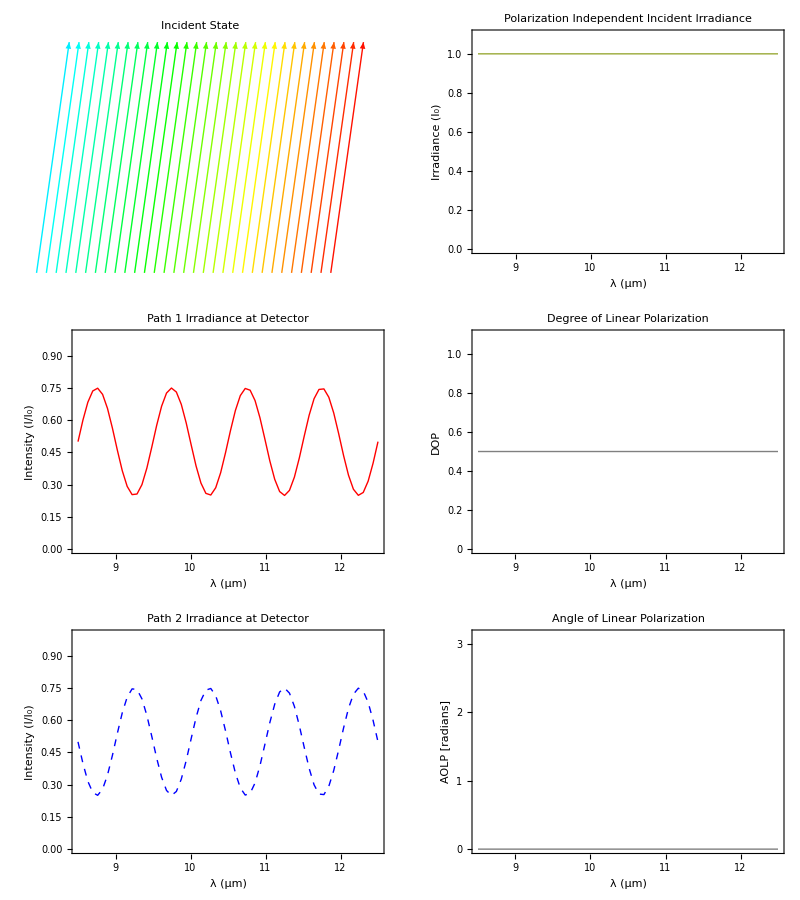

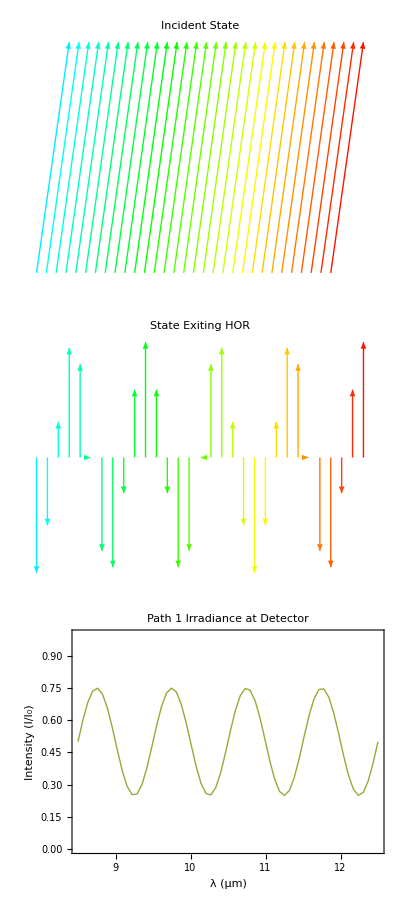

```mathematica
g1=Framed[{{pi,pint},{p1,pdop},{p2, paop}}//TableForm,FrameStyle->None]
g2=Framed[{pi,horexit,p1color}//TableForm,FrameStyle->None]
```

```mathematica
g=CompleteGraph[100];
exportDPI=2000;
```

```mathematica
Export["Z:\\Projects\\SWIRP\\Papers and Posters\\AMS 2019\\Figures\\polrotatopn_0.5_4545.png",g2,ImageResolution->exportDPI]
```

Z:\Projects\SWIRP\Papers and Posters\AMS 2019\Figures\polrotatopn_0.5_4545.png

## Calibration System MM Model

```mathematica
target1=2*lpPath1.{1,0,0,0}
```

{1,-1,0,0}

```mathematica
target2=2*lpPath2.{1,0,0,0}
```

{1,1,0,0}

```mathematica
target3={1,0,-1,0}
```

{1,0,-1,0}

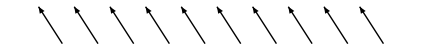
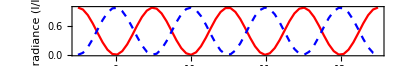

```mathematica
Framed[{Graphics[Table[{Black,Arrowheads[0.02],Arrow[{{0+3z,0},{0+3z,0}+{-1,1}}]},{z,8,12.5,.5}],Axes->{False,False},PlotLabel->"Incident State",LabelStyle->Directive[ Black],AspectRatio->1/13],ListLinePlot[{Table[{λ,(systemMMPath2[λ].target3)[[1]]},{λ,band}],Table[{λ,(systemMMPath1[λ].target3)[[1]]},{λ,band}]},PlotStyle->{Red,{Dashed,Blue}},AspectRatio->1/6,PlotLabel-> "Irradiance at Detector",PlotRange-> {0,1}, Axes->False ,Frame->{{True,False},{True,False}},FrameLabel->{{"Irradiance (I/I_0)",None},{"λ (μm)",None}},PlotLegends-> {"Path 1","Path 2"},LabelStyle->Directive[ Black],FrameTicks->All]
}//TableForm,FrameStyle->None]
```

## Full Data Reduction Simulation

### Make Sample Pixel Spectrum

```mathematica
fpasize=43;
```

```mathematica
λbins=Subdivide[8.5,12.5,fpasize];
```

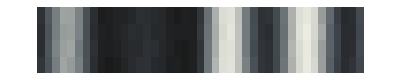

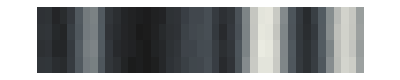

```mathematica
path1out=Table[Table[(systemMMReal1[λbins[[λ]]].stokes2[.8,0,λbins[[λ]]])[[1]]+RandomReal[{0,0.03}],{λ,1,43}],{i,1,4}];
path2out=Table[Table[(systemMMReal2[λbins[[λ]]].stokes2[.8,0,λbins[[λ]]])[[1]]+RandomReal[{0,0.03}],{λ,1,43}],{i,1,4}];
ArrayPlot[path1out,ColorFunction->"GrayTones"]
ArrayPlot[path2out,ColorFunction->"GrayTones"]
```

```mathematica
path1avg=Table[Mean[Transpose[path1out][[i]]],{i,1,42}];
path2avg=Table[Mean[Transpose[path2out][[i]]],{i,1,42}];
```

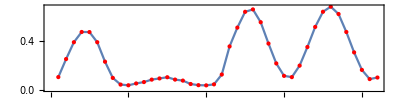

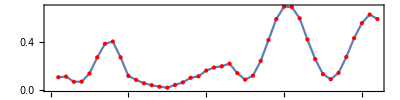

```mathematica
ListLinePlot[path1avg,AspectRatio->1/4,Mesh->All,MeshStyle->Directive[PointSize[Small],Red],Frame->True]
ListLinePlot[path2avg,AspectRatio->1/4,Mesh->All,MeshStyle->Directive[PointSize[Small],Red],Frame->True]
```

### Simulate Correction (not using calibration)

```mathematica
Dimensions[path1out]
```

{4,43}

```mathematica
path1outcorrected=Table[Table[path1out[[j,i]]/(QWPtrans[λbins[[i]]]*gratingEfficiency[λbins[[i]]]),{i,1,42}],{j,1,4}];
path2outcorrected=Table[Table[path2out[[j,i]]/(QWPtrans[λbins[[i]]]*gratingEfficiency[λbins[[i]]]),{i,1,42}],{j,1,4}];
```

```mathematica
radiometercorrected=Table[Table[path1out[[j,i]]+path2out[[j,i]],{i,1,42}],{j,1,4}];
```

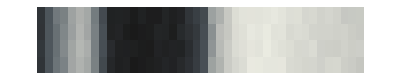

```mathematica
ArrayPlot[radiometercorrected,PlotLegends->Automatic,ColorFunction->"GrayTones"]
```

```mathematica
Dimensions[Transpose[radiometercorrected]]
```

```mathematica
avrirr=Table[Mean[Transpose[radiometercorrected][[i]]],{i,1,42}];
stfirr=Table[StandardDeviation[Transpose[radiometercorrected][[i]]],{i,1,42}];
avrirrdata=Table[{Mean[Transpose[radiometercorrected][[i]]],StandardDeviation[Transpose[radiometercorrected][[i]]]},{i,1,42}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

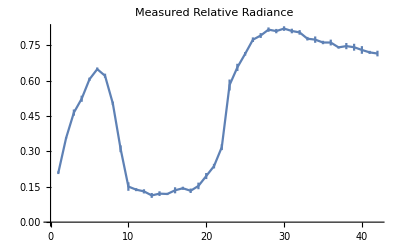

```mathematica
ErrorListPlot[avrirrdata,Joined->True,PlotLabel->"Measured Relative Radiance"]
```

```mathematica
path1corr=Table[Mean[Transpose[path1outcorrected][[i]]]/avrirr[[i]],{i,1,42}];
path2corr=Table[Mean[Transpose[path2outcorrected][[i]]]/avrirr[[i]],{i,1,42}];
```

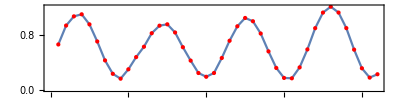

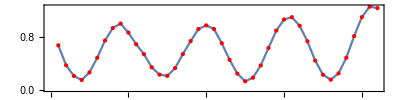

```mathematica
ListLinePlot[path1corr,AspectRatio->1/4,Mesh->All,MeshStyle->Directive[PointSize[Small],Red],Frame->True]
ListLinePlot[path2corr,AspectRatio->1/4,Mesh->All,MeshStyle->Directive[PointSize[Small],Red],Frame->True]
```